## Styling

```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
(*Styling of the text*)
st=Directive[Large,FontFamily->"Linux Libertine Display"];
stylize[text_]:=Style[text,st];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

```mathematica
Style[Text["caca"],BostonBlue]
```

caca

## Hamiltonians

### Definitions

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with free bc *)
ω=N [(Sqrt[5]-1)/2];
rot=28; (* rotate the sequence of couplings *)
fib[n_]:=IntegerPart[ω( n+1+rot)]-IntegerPart[ω (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];

hf[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with periodic bc *)
hpn[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
AppendTo[tbl,{1,F2}->tw];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Harper *)
hharp[p_,q_,ϕ_,λ_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*periodic boundary conditions*)AppendTo[hopping,{1,q}->-1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.λ Cos[2 π p i/q+ϕ],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfib[n_,ϕ_,λ_]:=hharp[Fibonacci[n-1],Fibonacci[n],ϕ,λ];
SetAttributes[hfib,Listable];
```

## Wavefunctions

### Wavefunctions: definitions.

We define general functions computing fractal dimensions from lists, rather than functions adapted to our specific case.

We compute χ_q^n(i)=Σ_a|ψ^n(i,a)|^(2q).
We define the local dimension of the wavefunctions:
D_q(i)=lim_(n→∞) 1/(q-1)(log(χ_q^n(i)))/(log(1/F_n))

```mathematica
(* wf is a list of numbers that are a priori the coefficients of a wavefunction. They can be coefficients in the position basis, for a given energy, or coefficients in the energy basis for a particular position. *)
WfD[wf_,q_]:=-(q-1)^-1 Log[Plus@@(Abs[wf]^(2q))]/Log[Length@wf]
```

```mathematica
(* a more precise way of computing the dimensions, using data from two systems of consecutive size *)
tauqxloc[int_,intN_,q_]:=-Log[(Total@(int^q))/(Total@(intN^q))]/Log[(Length@int)/(Length@intN)];
```

We compute the partition function (Γ_(τ,q))^n(i)=Σ_a(|ψ^n(i,a)|^(2q))/((Δ_a^n)^τ).
We define the local dimension of the wavefunctions:
τ_i(q) such that lim_(n→∞) ((Γ_(τ_i(q),q))^(n+1)(i))/((Γ_(τ_i(q),q))^n(i))=1

```mathematica
(* compute fractal dimension Subscript[D, q] from 2 lists of weights and box lengths, using the thermodynamic formalism *)
PartD[weights_,weightsN_,lengths_,lengthsN_,q_]:=Block[{gam,gamN,τ,τ0,q0},
gam=Plus@@((weights)^q0(lengths)^-τ);
gamN=Plus@@((weightsN)^q0(lengthsN)^-τ);
(* Subscript[D, q] *)
τ0=τ/.FindRoot[(gamN/gam/.q0->q)-1,{τ,0}];
τ0/(q-1)
]
```

#### Tree structure

After a renormalization step, a given site i of the n^th approximant becomes either molecular (in which case n becomes n-2) or atomic (n becomes n-3). 
We can thus associate to each site a unique “renormalization path”: the sequence of molecular/atomic sites that has led to it, starting from the trivial (F_n=1) chain and inflating it.

More details in the “renormalization_path.nb” file.

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
ClearAll[i,n];
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]

(* false when n<3 *)
test=#[[3]]≥3&;
(* take a site (i), a size (n) and return the renormalization path for this site *)
path[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]
(* compute the relative time spent on molecular sites (x) *)
xPath[i_,n_]:={i,StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]/n}
(* generate the whole (x) tree! *)
tree[n_]:=xPath[#,n]&/@ Range[Fibonacci[n]]
```

```mathematica
paths[n_]:=path[#,n]&/@Range[Fibonacci[n]]
```

```mathematica
(* count the numbers Subscript[n, A] and Subscript[n, M] *)
count[n_]:=Transpose[StringCount@@@({paths[n],#}&/@{"m","a"})]
```

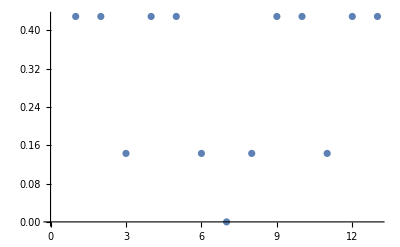

```mathematica
ListPlot[tree[7],Joined->False]
```

```mathematica
MapThread[2#1+3#2&,Transpose[count[9]]]
```

{8,8,7,8,8,7,8,7,8,8,7,8,8,7,8,7,8,8,7,8,7,8,8,7,8,8,7,8,7,8,8,7,8,8}

### Wavefunctions: computations

For a given ρ, q>0 and system size n, compute the D^x(x) dimensions, ie the D^x(i) dimensions averaged on all sites having the same x.

```mathematica
avDx[q_,vec_,val_,xvalues_,listPos_]:=Block[{DxList,xlist,avDx},
(* list fractal dimensions, indexed by site *)
DxList=WfD[#,q]&/@vec;

(* for each value of x compute the average - on positions corresponding to this x - fractal dimension *)
avDx=Mean[DxList[[#]]]&/@listPos;
(* return the average fractal dimension as a function of x *)
(*avDx=MapThread[{#1,#2}&,{xvalues,avDx}];*)
avDx
]
```

```mathematica
(* keep one processor free to prevent freeze *)
LaunchKernels[$ProcessorCount-1]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local]}

```mathematica
n=17;
ρ=0.15;
tol=10^-14;
(* compute wavefunctions and energies *)
{val,vec}=Eigensystem[hp[n,ρ,1.]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering[val]]];
(* drop small components *)
(*vec=Chop[vec,tol];*)

(* compute x for each site *)
xlist=tree[n+2];
(* drop the site labels, they are unecessary as x is indexed by increasing x label *)
xlist=Last@(Transpose[xlist]);

(* list all possible values of x *)
xvalues=Sort@DeleteDuplicates[xlist];
(* list all positions by increasing value of x *)
listPos=Flatten[Position[xlist,#]]&/@xvalues;
```

```mathematica
qlist=Range[0.,10,.3];
avdqlist=ParallelMap[avDx[#,vec,val,xvalues,listPos]&,qlist];
(* transpose to have x dependance as the first direction of the array *)
avdqlist=Transpose[avdqlist];
```

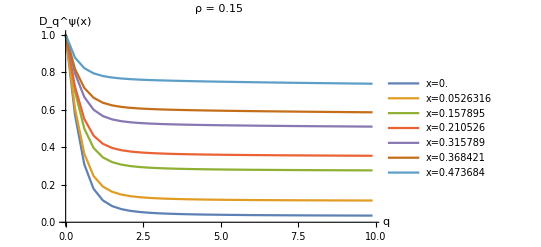

```mathematica
ListPlot[MapThread[{#1,#2}&,{qlist,#}]&/@avdqlist,Joined->True,AxesStyle->st,AxesLabel->{"q","D_q^ψ(x)"},PlotLegends->("x="<>ToString[N[#]]&)/@xvalues,PlotLabel->stylize["ρ = "<>ToString[ρ]]]
```

### Comparison with theory

#### Theoretical fomulas

```mathematica
ω=N[(√5-1)/2];
lb[ρ_]:=(Sqrt[(1+ρ^2)^4+4 ρ^4]-(1+ρ^2)^2)/(2 ρ^4);
γ[ρ_,q_]:=1/(1+ρ^q);
lambda[ρ_,q_]:=(1+γ[ρ,q] ρ^2-√(1+(γ[ρ,q] ρ^2)^2))/(2γ[ρ,q] ρ^2);
wfdth[ρ_,q_,x_,n_]:=If[q<3,-(n+2)(x Log[lambda[ρ,q]^q/lambda[ρ^q,q]]+(1-2x)/3 Log[lb[ρ]^q/lb[ρ^q]])/((q-1)Log[Fibonacci[n+2]]),d2th[ρ,q,x,n]];
d2th[ρ_,q_,x_,n_]:=-(n+2)(x Log[lambda[ρ,q]^q]+(1-2x)/3 Log[lb[ρ]^q]+x Log[2])/((q-1)Log[Fibonacci[n+2]]);
(* in the finite size case, 3 Subscript[n, A]+ 2 Subscript[n, M] ≠ n, so that it is more accurate to replace x by Subscript[n, M] and Subscript[n, A] in the fractal dimensions *)
dfinite[ρ_,q_,{nm_,na_},n_]:=If[q<3,-(nm/(n+2) Log[lambda[ρ,q]^q/lambda[ρ^q,q]]+na/(n+2) Log[lb[ρ]^q/lb[ρ^q]])/((q-1)Log[Fibonacci[n+2]^(1/(n+2))]),d2th[ρ,q,nm/(n+2),n]];
```

#### Data averaged per value of x

```mathematica
ct=DeleteDuplicates[count[n+2]]
```

{{9,0},{7,1},{6,2},{4,3},{3,4},{1,5},{0,6}}

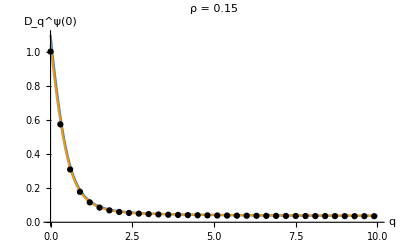

```mathematica
Plot[{wfdth[ρ,q,0,n],dfinite[ρ,q,{0,6},n]},{q,0,10},PlotRange->{0,1.1},Epilog->{AbsolutePointSize[4.5],Point@MapThread[{#1,#2}&,{qlist,avdqlist[[1]]}]},AxesStyle->st,AxesLabel->{"q","D_q^ψ(0)"},PlotLabel->stylize["ρ = "<>ToString[ρ]]]
```

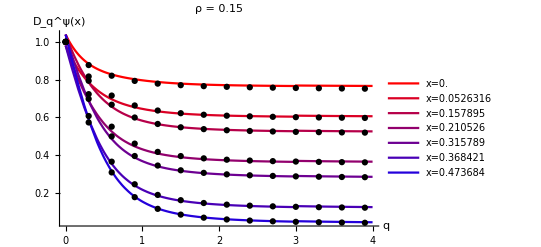

```mathematica
qdqlist=MapThread[{#1,#2}&,{qlist,#}]&/@avdqlist;
plotfunc[q_]:=dfinite[ρ,q,#,n]&/@ct;
t=Table[Blend[{Red,Blue},i],{i,0,1,1/Length@xvalues}];
Plot[Evaluate[plotfunc[q]],{q,0,4},PlotRange->All,Epilog->{AbsolutePointSize[4.5],Point/@qdqlist},AxesStyle->st,AxesLabel->{"q","D_q^ψ(x)"},PlotLabel->stylize["ρ = "<>ToString[ρ]],PlotLegends->("x="<>ToString[N[#]]&)/@xvalues,PlotStyle->t]
```

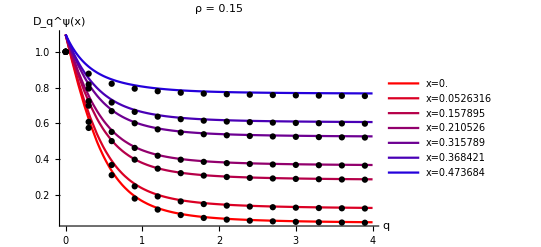

```mathematica
qdqlist=MapThread[{#1,#2}&,{qlist,#}]&/@avdqlist;
plotfunc[q_]:=wfdth[ρ,q,#,n]&/@xvalues;
t=Table[Blend[{Red,Blue},i],{i,0,1,1/Length@xvalues}];
Plot[Evaluate[plotfunc[q]],{q,0,4},PlotRange->All,Epilog->{AbsolutePointSize[4.5],Point/@qdqlist},AxesStyle->st,AxesLabel->{"q","D_q^ψ(x)"},PlotLabel->stylize["ρ = "<>ToString[ρ]],PlotLegends->("x="<>ToString[N[#]]&)/@xvalues,PlotStyle->t]
```

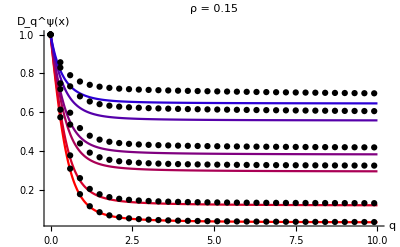

```mathematica
Export[dir<>"data/individual_wf_dimensions.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/individual_wf_dimensions.pdf

#### Non averaged data

```mathematica
n=16;
ρ=0.1;
tol=10^-14;
(* compute wavefunctions and energies *)
{val,vec}=Eigensystem[hp[n,ρ,1.]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering[val]]];
```

```mathematica
(* middle of the energy spectrum *)
mid=(Fibonacci[n+2]+1)/2;
(* fractal dimensions of the wavefunction at the center of the spectrum *)
qlist=Range[0.,10,.3];
d0=WfD[vec[[mid]],#]&/@qlist;
d0q=MapThread[{#1,#2}&,{qlist,d0}];
```

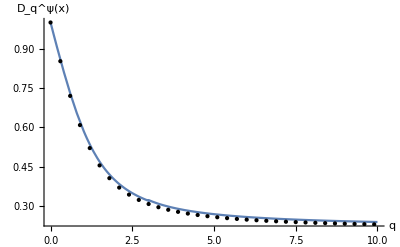

```mathematica
Plot[{wfdth[ρ,q,0,10^4]},{q,0,10},PlotRange->Full,Epilog->Point@d0q,AxesStyle->st,AxesLabel->{"q","D_q^ψ(x)"}]
```

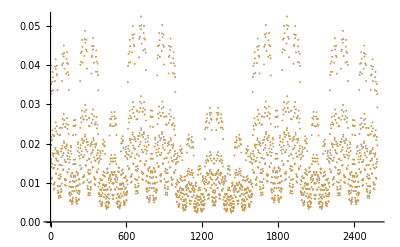

```mathematica
(* /!\ to have a completely bipartite lattice (and therefore have |ψ(1)| = |ψ(-1)|, we need Subscript[F, n+2] to be even *)
ListPlot[{Abs[vec[[1]]],Abs[vec[[-1]]]},PlotRange->All]
```

```mathematica
(* edges of the energy spectrum /!\ Subscript[F, n+2] needs to be even *)
edge=1;
(* fractal dimensions of the wavefunction at the edges of the spectrum *)
qlist=Range[0.,10,.3];
ded=WfD[vec[[edge]],#]&/@qlist;
dedq=MapThread[{#1,#2}&,{qlist,ded}];

(* now we compute the max value of x *)
(* compute x for each site *)
xlist=tree[n+2];
(* drop the site labels, they are unecessary as x is indexed by increasing x label *)
xlist=Last@(Transpose[xlist]);
(* list all possible values of x *)
xvalues=Sort@DeleteDuplicates[xlist];
xmax=xvalues[[-1]];
```

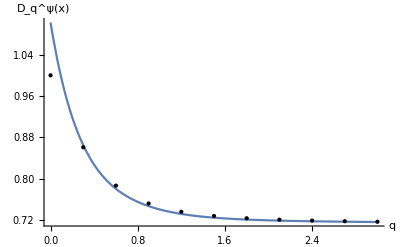

```mathematica
Plot[{wfdth[ρ,q,xmax,n]},{q,0,3},PlotRange->Full,Epilog->Point@dedq,AxesStyle->st,AxesLabel->{"q","D_q^ψ(x)"}]
```

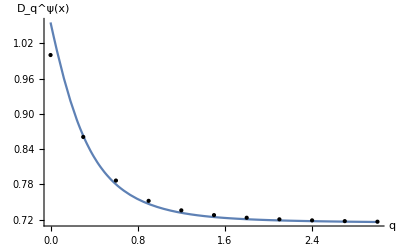

```mathematica
Plot[{dthtest[ρ,q,xmax,0,n]},{q,0,3},PlotRange->Full,Epilog->Point@dedq,AxesStyle->st,AxesLabel->{"q","D_q^ψ(x)"}]
```

### Tests

D_1 = (1-ρ Log ρ d/(d ρ))(x Log λ + (1-2x)/3 Log lb )

```mathematica
Block[{x=10,ρ=12.},
{x Log[lambda[ρ,1]]+(1-2x)/3 Log[lb[ρ]]-x ρ Log[ρ](Derivative[1,0][lambda][ρ,1])/lambda[ρ,1]-(1-2x)/3 ρ Log[ρ](Derivative[1][lb][ρ])/lb[ρ],Log[ω]dth[ρ,0.999999,x]}]
```

{-5.41274,-5.41273}

λ^ll

```mathematica
(-s(1+ r )+√(s^2(1+r)^2-2(- c(1+r)+s(1+2r))))/(2(c(1+r)-s(1+2r)))/.{s->1,c->1,r->1/2}
```

3/2-(√5)/2

```mathematica
(-s(1+ r )+√(s^2(1+r)^2-2(- c(1+r)+s(1+2r))))/(2(c(1+r)-s(1+2r)))/.{r->γ r^2};
%/.{s->1-r^2/2,c->1+r^2/2};
Series[%,{r,0,4}]
```

1/2-(γ r^2)/4+O[r]^5

```mathematica
(* generate λ^ll *)
(-s(1+ r )+√(s^2(1+r)^2-2(- c(1+r)+s(1+2r))))/(2(c(1+r)-s(1+2r)))/.{r->γ[r,q] r^2};
%/.{s->1-r^2/2,c->1+r^2/2};
```

```mathematica
λll[r_,q_]:=(-(1-r^2/2) (1+r^2/(1+r^q))+√((1-r^2/2)^2 (1+r^2/(1+r^q))^2-2 (-(1+r^2/2) (1+r^2/(1+r^q))+(1-r^2/2) (1+(2 r^2)/(1+r^q)))))/(2 ((1+r^2/2) (1+r^2/(1+r^q))-(1-r^2/2) (1+(2 r^2)/(1+r^q))))
```

```mathematica
Series[λll[r,10],{r,0,4}]
```

1/2-r^2/4+O[r]^5

λ^lc

```mathematica
c[r_]:=1+r^2/2;
s[r_]:=1-r^2/2;
λlc[r_,q_]:=(c[r](1+r^2)+s[r]+lb[r](s[r](1+2 r^2)-c[r](1+r^2)))^-1
```

Interestingly, λ^ll and λ^lc have different corrections at order 4 in ρ

```mathematica
Series[λlc[r,10],{r,0,4}]
```

1/2-r^2/4+(3 r^4)/8+O[r]^5

Fractal dimensions

```mathematica
dthtest[ρ_,q_,x_,y_,n_]:=-(n+2)((x-y) Log[λll[ρ,q]^q/λll[ρ^q,q]]+y Log[λlc[ρ,q]^q/λlc[ρ^q,q]]+(1-2x)/3 Log[lb[ρ]^q/lb[ρ^q]])/((q-1)Log[Fibonacci[n+2]]);
```